## ALP-fermion

### Model description

```mathematica
LLPsel="ALP-fermion";
ModelDescription[LLPsel]=Row[{"Axion-like particle a with the phenomenological Lagrangian L = c_f(SubscriptBox[d, μ]a)/f_af̄γ^μγ_5f. The Lagrangian is defined at some scale Λ, with c_G, f_a being the couplings (f_a is in general unrelated to Λ). f is the SM fermion field. The particula value c_f = 1 at Λ = 1 TeV is called BC10 within PBC benchmarking (1901.09966). In this model, initially, ALPs universally couple to fermions; however, the RG flow down to scales of interest destroys the universality. See 2110.10698, 2310.03524, and 2501.04525 for the phenomenology description"}];
filepheno=FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology","ModelDescriptors.mx"}];
rowtoadd={LLPsel,ModelDescription[LLPsel]};
If[!FileExistsQ[filepheno],
file={rowtoadd};
,
file=Import[filepheno,"MX"];
file=Join[Select[file,#[[1]]!=LLPsel&],{rowtoadd}];
]
Export[filepheno,SortBy[file,#[[1]]&],"MX"];
```

### Importing lifetime

```mathematica
LLPsel="ALP-fermion";
(*List of widths of the ALP into various final states*)
DecayWidthsDataTemp=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology",LLPsel,"decay widths","Widths-model-Fermion universal-scale-1000.-GeV.m"}],"MX"];
DecayWidthsDataTemp2=DecayWidthsDataTemp[[4]];
{Table[i,{i,1,Length[DecayWidthsDataTemp2[[1]]],1}],DecayWidthsDataTemp2[[1]]}//TableForm
DecayWidthsData=Drop[DecayWidthsDataTemp2,3];
(*Total decay width and lifetime*)
totalwidthdata=DecayWidthsData[[All,{1,-1}]];
descr="Default";
cτLLP[LLPsel,descr,mLLP_,y_]=chbar/((1/(2vh))^2 y^2 Interpolation[DecayWidthsData[[All,{1,-1}]],InterpolationOrder->1][mLLP]);
couplingSymbol[LLPsel]=y;
DecayDescriptionExplanation[LLPsel,descr]="Description of hadronic width of ALPs following 2310.03524";
descr="PBC description";
cτLLP[LLPsel,descr,mLLP_,y_]=chbar/((1/(2vh))^2 y^2 Interpolation[Join[DecayWidthsData[[All,{1}]],DecayWidthsData[[All,{2}]]+DecayWidthsData[[All,{4}]]+DecayWidthsData[[All,{5}]],2],InterpolationOrder->1][mLLP]);
DecayDescriptionExplanation[LLPsel,descr]="Description of hadronic width following the PBC report 1901.09966. It was widely used in the past";
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34
m_a, GeV | 2e | 2γ | 2μ | 2τ | 2b | 2c | 2d | 2G | 2s | 2t | 2u | 2π^+2π^- | 2ϕ | 2ω | 3π^0 | 3η | K^(*0)(K̄)^(*0) | K^0(K̄)^0π^0 | K^(*+)K^(*-) | K^-K^0π^+ | K^+K^-π^0 | K^+(K̄)^0π^- | γπ^+π^- | η2π^0 | ηπ^+π^- | π^+π^-2π^0 | π^+π^-π^0 | ωπ^+π^- | η'2π^0 | η'π^+π^- | Non-hadronic, total | Hadronic, total | Total

### List of decay processes and sets of decay products for them, branching ratios

All processes with at least two charged/neutral particles:

{2e,2μ,2τ,2γ,π^+π^-π^0,γπ^+π^-,π^+π^-2π^0,2π^+2π^-,η2π^0,ηπ^+π^-,K^(*+)K^(*-),K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,ωπ^+π^-,3π^0,η'2π^0,η'π^+π^-,2ω,Jets-GG,Jets-cc,Jets-ss}

All processes with at least two charged particles:

{2e,2μ,2τ,π^+π^-π^0,γπ^+π^-,π^+π^-2π^0,2π^+2π^-,η2π^0,ηπ^+π^-,K^(*+)K^(*-),K^(*0)(K̄)^(*0),K^0(K̄)^0π^0,K^-K^0π^+,K^+K^-π^0,K^+(K̄)^0π^-,ωπ^+π^-,η'2π^0,η'π^+π^-,2ω,Jets-GG,Jets-cc,Jets-ss}

Processes with jets:

{Jets-GG,Jets-cc,Jets-ss}

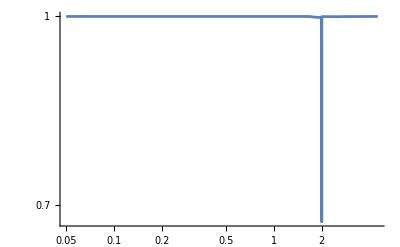

```mathematica
LLPsel="ALP-fermion";
BrRatiosALPfermionData[ma_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology",LLPsel,"decay widths/Br-ratios-SensCalc-model-Fermion universal-scale-1000.-GeV.m"}],"MX"];
(*List of all representative processes*)
ProcessesList[LLPsel,"True"]=BrRatiosALPfermionData[ma][[1]]/.{"Jets"->"Jets-GG"};
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
procsel=ProcessesList[LLPsel,"True"][[i]];
ListBrRatiosTemp[LLPsel,mLLP_,procsel,"Default"]=ListBrRatios[LLPsel,mLLP_,procsel,"Default"]=BrRatiosALPfermionData[mLLP][[3]][[i]];
ListDecayProducts[LLPsel,procsel]=BrRatiosALPfermionData[ma][[2]][[i]];
JetsPresence[LLPsel,procsel]=If[MemberQ[{"Jets-ss","Jets-cc","Jets-GG"},procsel]==True,"Yes","No"]
,{i,1,Length[BrRatiosALPfermionData[mLLP][[3]]],1}]
ProcessesList[LLPsel,"False"]=procListnoecal[LLPsel];
Print["All processes with at least two charged/neutral particles:"]
ProcessesList[LLPsel,"True"]
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatiosTemp[LLPsel,mN,pr,"Default"],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,4.5},PlotRange->All]
```

```mathematica
(*malist=Table[ma,{ma,0.3,5.2,0.001}];
tabbr=(Join[Partition[malist,1],Table[(BrRatiosALPfermionData[ma][[3]])/Total[BrRatiosALPfermionData[ma][[3]]],{ma,malist}],2]/. x_Real/;Abs[x]<10^-15:>0.)//N//Developer`ToPackedArray;
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"temp1","br-ratios-BC10.txt"}],tabbr,"Table"]*)
```

#### Old description from 1901.09966 - no hadronic decays

{2e,2μ,2τ}

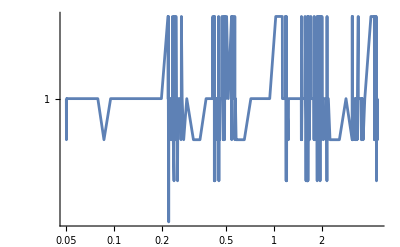

```mathematica
LLPsel="ALP-fermion";
descr="PBC description";
(*List of all representative processes*)
procselTemp=Select[ProcessesList[LLPsel,"True"],MemberQ[{"2e","2μ","2τ"},#]&]
(*The mass above which all hadronic decays are approximated by decays into jets*)
Do[
Module[{procsel=ProcessesList[LLPsel,"True"][[i]]},
If[MemberQ[{"2e","2μ","2τ"},procsel],
ListBrRatiosTemp[LLPsel,mLLP_,procsel,descr]=ListBrRatios[LLPsel,mLLP_,procsel,descr]=ListBrRatios[LLPsel,mLLP,procsel,"Default"]/((ListBrRatios[LLPsel,mLLP,"2e","Default"]+ListBrRatios[LLPsel,mLLP,"2μ","Default"]+ListBrRatios[LLPsel,mLLP,"2τ","Default"])//Simplify);
,
ListBrRatios[LLPsel,mLLP_,procsel,descr]=ListBrRatiosTemp[LLPsel,mLLP_,procsel,descr]=0.
]
]
,{i,1,Length[ProcessesList[LLPsel,"True"]],1}]
LogLogPlot[{Evaluate[Sum[ListBrRatiosTemp[LLPsel,mN,pr,descr],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,4.5},PlotRange->All]
listDecayDescriptions[LLPsel]=Select[Transpose[Keys[DownValues@ListBrRatios][[All,1,#]]&/@{1,-1}],#[[1]]==LLPsel&][[All,2]]//DeleteDuplicates
```

### Squared matrix elements

```mathematica
LLPsel="ALP-fermion";
MatrixElementsALPfermionList[ma_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology",LLPsel,"decay widths/Matrix-elements-squared-model-Fermion universal-scale-1000.-GeV.m"}],"MX"];
Do[
Msquared3BodyLLP[LLPsel,MatrixElementsALPfermionList[ma][[1]][[i]],E1_,E3_,mLLP_,"Default"]=Msquared3BodyLLP[LLPsel,MatrixElementsALPfermionList[ma][[1]][[i]],E1_,E3_,mLLP_,"PBC description"]=MatrixElementsALPfermionList[mLLP][[3]][[i]]
,{i,1,Length[MatrixElementsALPfermionList[ma][[3]]],1}];
```